#### Notes

Maybe we can test random weights for some number of attempts then skip to next if none are found. This random search would reduce memory complexity of the algorithm. 
		First: Test random weights to reduce Graph List
	 	Second: Complete Test of all weights
	 	Third: ?
	
	Understanding the relationships between graphs would be nice. We could test the graphs in order of inclusion as a subgraph. So Construct a Poset of the graphs where the order is by inclusion as isomorphic subgraphs ( Not sure if this actually leads to a Poset structure but the idea is still there). Then perform tests according to the ordering.

#### Code

```mathematica
(* Brute force construction of all Graphs on n vertices up to Isomorphism*)
allEdges[n_]:=Flatten[Table[UndirectedEdge[i,j],{i,1,n},{j,i+1,n}]];
allConnected[n_]:=Select[Map[Graph[Range[n],#,VertexLabels->Automatic]&,Subsets[allEdges[n]]],ConnectedGraphQ];
allConnectedUpToIso[n_]:=DeleteDuplicates[allConnected[n],IsomorphicGraphQ];
(*Helper Functions*)
PerfectDistanceQ[G_]:=Union[Flatten[Round[GraphDistanceMatrix[G]]]] == Range[0,Binomial[VertexCount[G],2]]
WeightsList[G_]:=Flatten[Permutations[#]&/@Select[Subsets[Range[Binomial[VertexCount[G],2]],{EdgeCount[G]}],MemberQ[#,1]&&MemberQ[#,2]&],1]
```

```mathematica
(*Construct Graph Sets*)
vertex5=allConnectedUpToIso[5];
(*vertex6=allConnectedUpToIso[6];*)
```

{0.727614,Null}

Minimal Perfect Distance Graphs:

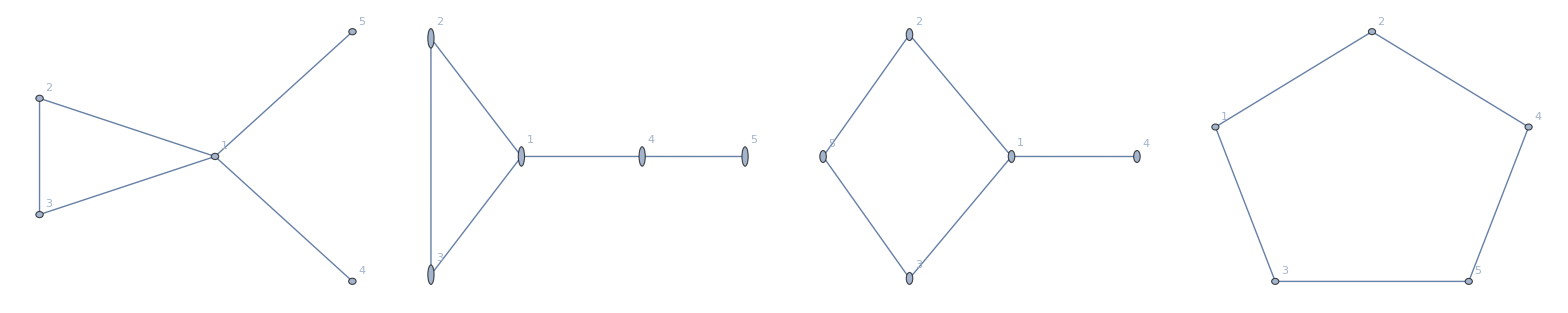

Not Perfect Distance Graphs:

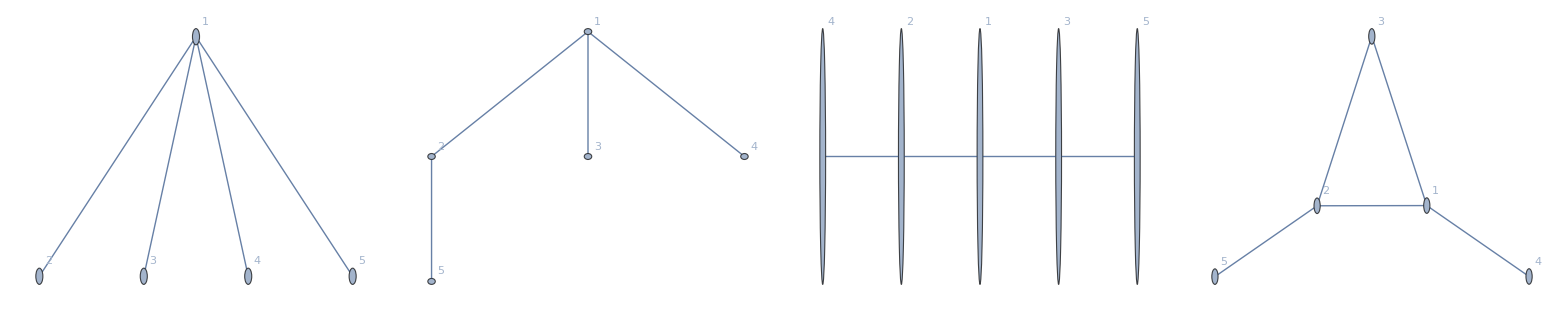

```mathematica
(*
 vertex5 should take around a second
vertex6 took around 8 minutes on my laptop
*)
(*CHOOSE SET OF GRAPHS TO TEST*)
GraphList = vertex5;

MinimalPerfectDistanceGraphs = {};
NotPerfectDistanceGraphs = {};

AbsoluteTiming[
While[Length[GraphList]>0,
G = First[GraphList];
GraphList = Delete[GraphList,1];

(* Test weights until a PDG is found or weights exausted*)
(*PerfectDistanceGraph = Null if G does not support a perfect distance weighting*)
WL = WeightsList[G];

PerfectDistanceGraph = Catch[Do[If[PerfectDistanceQ[Graph[EdgeList[G],EdgeWeight->WL[[j]]]],Throw[G]],{j,1,Length[WL]}]];

(*Update MPDG and NPD: Comparisions to Null are probelmatic*)
If[Head[PerfectDistanceGraph]==Graph, AppendTo[MinimalPerfectDistanceGraphs,PerfectDistanceGraph]];
If[PerfectDistanceGraph==Null,AppendTo[NotPerfectDistanceGraphs,G]];

(*Trim Graph List*)
GraphList = Select[GraphList,Not[IsomorphicSubgraphQ[PerfectDistanceGraph,#]]&];
];
]

Print["Minimal Perfect Distance Graphs: "]
TableForm[MinimalPerfectDistanceGraphs,TableDirections->Row]

Print["Not Perfect Distance Graphs: "]
TableForm[NotPerfectDistanceGraphs,TableDirections->Row]
```